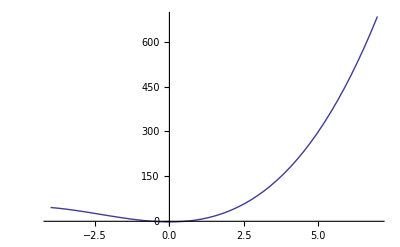
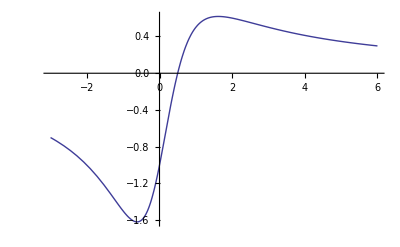
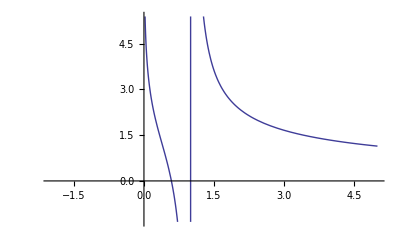
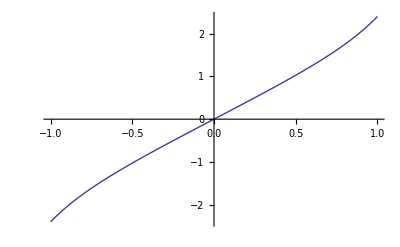
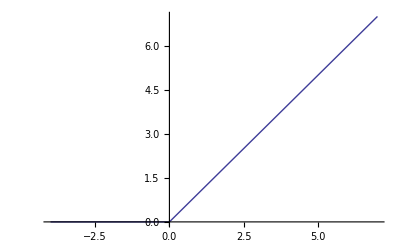
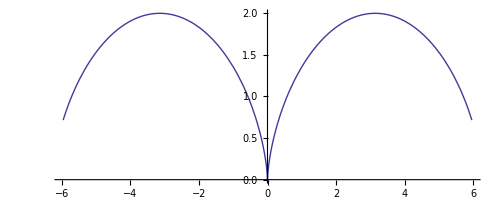
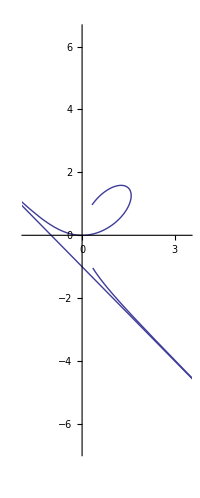
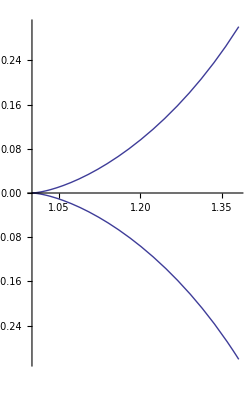
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{Plot[x^3+7 x^2-2,{x,-4,7}],Plot[(2x-1)/(x^2+1),{x,-3,6}],Plot[(√x+Log[2,x])/(x-1),{x,-2,5}],Plot[Sin[x]+Tan[x],{x,-1,1}],Plot[1/2*(x+Abs[x]),{x,-4,7}],ParametricPlot[{t-Sin[t],1-Cos[t]},{t,-5,5}] ,ParametricPlot[{2*(Cos^2)[t],2*(Sin^2)[t]},{t,-4,4}],ParametricPlot[{(3*t)/(1+t^3),(3*t^2)/(1+t^3)},{t,-3,3}],ParametricPlot[{Cos[t]+t*Sin[t],Sin[t]-t*Cos[t]},{t,-1,1}],ParametricPlot[{2^t+2^-t,2^r-2^-t},{t,-9,9}],PolarPlot[π/φ,{φ, -3π,3π}],PolarPlot[(Sech^2)[φ/2],{φ,-3,3}],PolarPlot[10*Sin[3φ],{φ,-1,1}],PolarPlot[1-Cos[φ],{φ,-2,2}],PolarPlot[ⅇ^φ,{φ,-4,4}],ContourPlot[x^2+y^2==4,{x,-1,1},{y,-1,1}],ContourPlot[(x^2+y^2)^2==x^2-y^2,{x,-2,2},{y,-2,2}],ContourPlot[x^2/100+y^2/64==1,{x,-2,2},{y,-2,2}],ContourPlot[x^3+y^3-3*x*y,{x,-4,4},{y,-4,4}],ContourPlot[x*y==2,{x,-2,2},{y,-2,2}]}
```

```mathematica
{Plot3D[x^2/4+y^2,{x,-1,1},{y,-1,1}],Plot3D[Sin[x*y],{x,-2,2},{y,-2,2}],Plot3D[Tan[x+2*y],{x,-3,3},{y,-3,3}],ContourPlot3D[x^2+y^2+z^2,{x,-4,4},{y,-4,4},{z,-4,4}],ContourPlot3D[x^2/4+y^2/9-z^2,{x,-5,5},{y,-5,5},{z,-5,5}],ParametricPlot3D[{Cos[φ]*(3+Cos[θ]),Sin[φ]*(3+Cos[θ]),Sin[2*θ]},{φ,-6,6},{θ,-6,6}],ParametricPlot3D[{φ^2*Cos[φ]*(5+Cos[φ+θ]),φ^2*Sin[φ]*(5+Cos[φ+θ]),φ^2*Sin[φ+θ]},{φ,-7,7},{θ,-7,7}]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

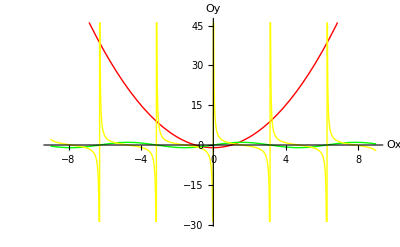
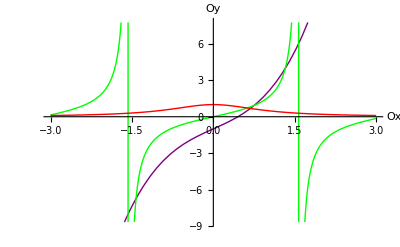
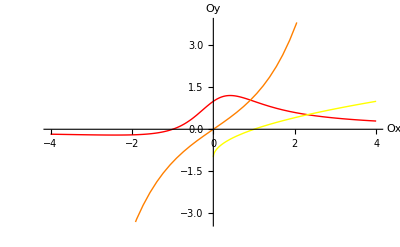
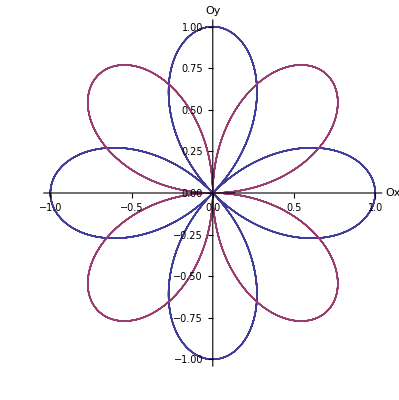
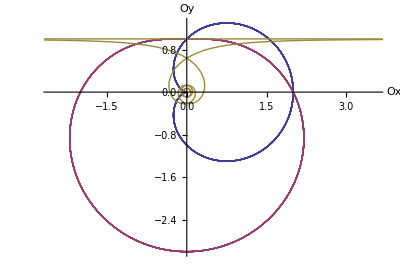
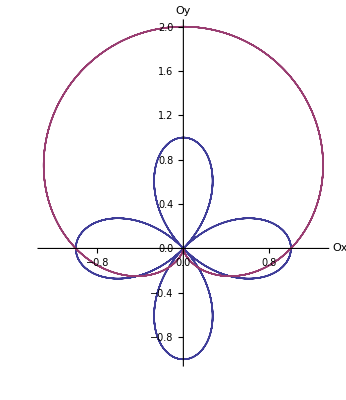

```mathematica
{Plot[{x^2-1,Sin[x],Cot[x]},{x,-9,9},PlotStyle->{Red,Green,Yellow},AxesLabel->{"Ox","Oy"}],Plot[{x^3+2x-1,Tan[x],1/(x^2+1)},{x,-3,3},PlotStyle->{Purple,Green,Red},AxesLabel->{"Ox","Oy"}],
Plot[{Log[e,x],(x+1)/(x^2+1),√x-1,Sinh[x]},{x,-4,4},PlotStyle->{Orange,Red,Yellow},AxesLabel->{"Ox","Oy"}],PolarPlot[{Cos[2φ],Sin[2φ]},{φ,-5π,5π},AxesLabel->{"Ox","Oy"}],PolarPlot[{1+Cos[φ],2-Sin[φ],1/φ},{φ,-5π,5π},AxesLabel->{"Ox","Oy"}],PolarPlot[{Cos[2φ],1+Sin[φ]},{φ,-5π,5π},AxesLabel->{"Ox","Oy"}]}
```

```mathematica
{Plot3D[x^2+y^2-1,{x,-2,2},{y,-2,2}],Plot3D[x^3+y^3-1,{x,-3,3},{y,-3,3}],Plot3D[x^4+y^4-1,{x,-4,4},{y,-4,4}],ParametricPlot3D[{Cos[φ+4ψ],Sin[ψ],Cos[ψ]*Sin[φ]},{φ,-2π,2π},{ψ,-2π,2π}],ParametricPlot3D[{Sin[2ψ+4φ],2*Cos[4φ+5ψ],Sin[ψ+φ]*Cos[3ψ+2φ]},{φ,-5π,5π},{ψ,-5π,5π}],ParametricPlot3D[{Sin[8ψ+4φ]*Cos[5ψ+3φ],3*Sin[3ψ]*Cos[4φ],Cos[2ψ]},{ψ,-π,π},{φ,-π,π}],ContourPlot3D[x^2+y^3-x*y+z^3-x*y^3==1,{x,-3,3},{y,-3,3},{z,-3,3}],ContourPlot3D[x^4+y^2+x*y*z-y^2*x^3*z^4+x*y*z==1,{x,-2,2},{y,-2,2},{z,-2,2}],ContourPlot3D[x^2+y^2+z^2+3*x*y*z==1,{x,-5,5},{y,-5,5},{z,-5,5}]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

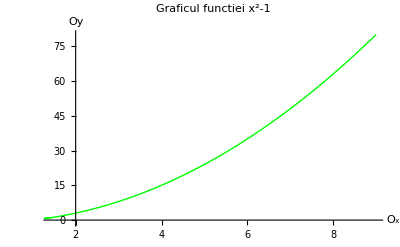

```mathematica
Needs["PlotLegends`"]
Plot[{x^2-1},{x,9,1,2/3,1/4,√2},AxesLabel->{"O_x","Oy"},PlotStyle->Green,PlotLabel->"Graficul functiei x^2-1",PlotLegend->{"y=x^2-1"}]
```

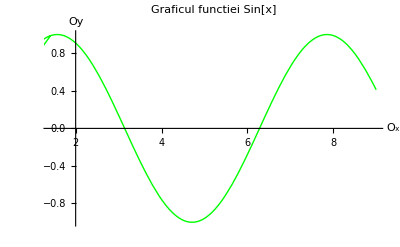

```mathematica
Needs["PlotLegends`"]
Plot[{Sin[x]},{x,9,1,2/3,1/4,√2},AxesLabel->{"O_x","Oy"},PlotStyle->Green,PlotLabel->"Graficul functiei Sin[x]",PlotLegend->{"y=Sin[x]"}]
```

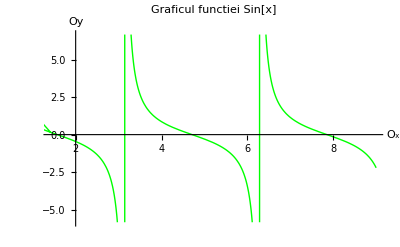

```mathematica
Needs["PlotLegends`"]
Plot[{Cot[x]},{x,9,1,2/3,1/4,√2},AxesLabel->{"O_x","Oy"},PlotStyle->Green,PlotLabel->"Graficul functiei Sin[x]",PlotLegend->{"y=Cot[x]"}]
```

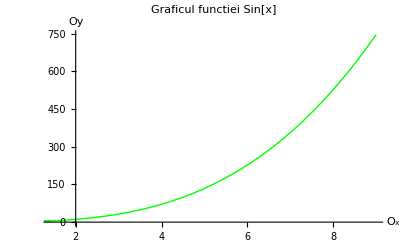

```mathematica
Needs["PlotLegends`"]
Plot[{x^3+2x-1},{x,9,1,2/3,1/4,√2},AxesLabel->{"O_x","Oy"},PlotStyle->Green,PlotLabel->"Graficul functiei Sin[x]",PlotLegend->{"y=x^3+2x-1"}]
```

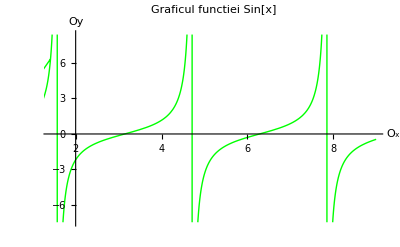

```mathematica
Needs["PlotLegends`"]
Plot[{Tan[x]},{x,9,1,2/3,1/4,√2},AxesLabel->{"O_x","Oy"},PlotStyle->Green,PlotLabel->"Graficul functiei Sin[x]",PlotLegend->{"y=Tan[x]"}]
```

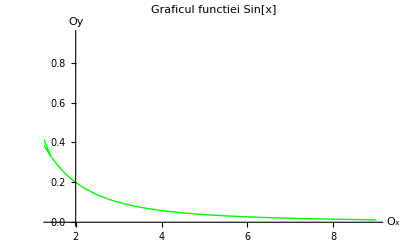

```mathematica
Needs["PlotLegends`"]
Plot[{1/(x^2+1)},{x,9,1,2/3,1/4,√2},AxesLabel->{"O_x","Oy"},PlotStyle->Green,PlotLabel->"Graficul functiei Sin[x]",PlotLegend->{"y=1/x^2"}]
```

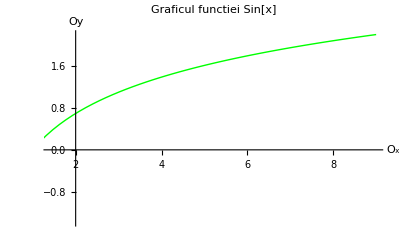

```mathematica
Needs["PlotLegends`"]
Plot[{Log[ⅇ,x]},{x,9,1,2/3,1/4,√2},AxesLabel->{"O_x","Oy"},PlotStyle->Green,PlotLabel->"Graficul functiei Sin[x]",PlotLegend->{"y=Log[ⅇ,x]"}]
```

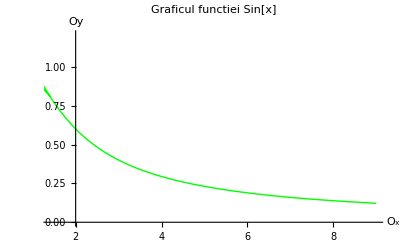

```mathematica
Needs["PlotLegends`"]
Plot[{(x+1)/(x^2+1)},{x,9,1,2/3,1/4,√2},AxesLabel->{"O_x","Oy"},PlotStyle->Green,PlotLabel->"Graficul functiei Sin[x]",PlotLegend->{"y=(x + 1)/x^2"}]
```

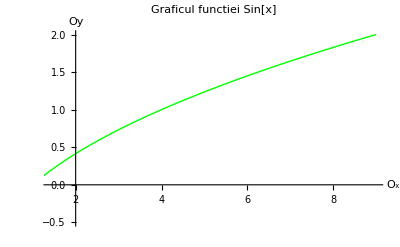

```mathematica
Needs["PlotLegends`"]
Plot[{√x-1},{x,9,1,2/3,1/4,√2},AxesLabel->{"O_x","Oy"},PlotStyle->Green,PlotLabel->"Graficul functiei Sin[x]",PlotLegend->{"y=√x-1"}]
```

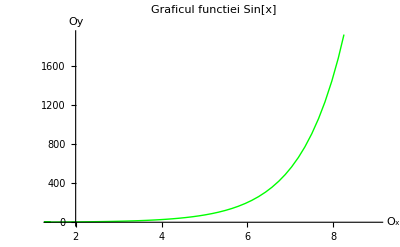

```mathematica
Needs["PlotLegends`"]
Plot[{Sinh[x]},{x,9,1,2/3,1/4,√2},AxesLabel->{"O_x","Oy"},PlotStyle->Green,PlotLabel->"Graficul functiei Sin[x]",PlotLegend->{"y=Sinh[x]"}]
```